```mathematica
Clear["Global`*"]
```

```mathematica
Import[NotebookDirectory[]<>"../models/SimplifyFunctions.m"]
Import[NotebookDirectory[]<>"../models/QuaternionAlgebra.m"]
Import[NotebookDirectory[]<>"DatasetFunctions.m"];

ParallelEvaluate[Off[FullSimplify::time]];
ParallelEvaluate[Off[Simplify::time]];
ParallelEvaluate[Off[Simplify::gtime]];
```

```mathematica
ToGoodC[exp_]:=Module[{oexp}, oexp=Experimental`OptimizeExpression[exp];
If[Dimensions [StringPosition[ToString[InputForm[oexp]],"Compile"],1][[1]]>0,Block[{ locals, code},{locals,code}=ReleaseHold[(Hold@@oexp)/.Verbatim[Block][vars_,seq_]:>{vars,Hold[seq]}];ToString[CForm[code]]]
, ToString[CForm[exp]]]]
MyStringWrite[str_,file_]:=Module[{stream},stream=OpenWrite[file];WriteString[stream,str];Close[stream];]
```

# Dataset definition

```mathematica
X = 4;
Y = 4;
Z=2;
tloop = 60;
sox=0;
soy=0.25;
soz=0;
dt=1/10; (* time difference between first and second pose exports *)

(*
x[t_]:=X Sin[4π /tloop t];
y[t_]:=Y Sin[2 π /tloop t];
z[t_]:=Z Cos[4 π /tloop t ]/4;
*)
(* otto 
x[t]:= X Cos[2 π  (t/tloop)^2];
y[t]:= Y Sin[4 π (t/tloop)^2];
z[t]:= Z Cos[4 π(t/tloop)^2]; 
*)

(* uniformly accelerated circular motion with alpha 0.005 *)
x[t]:= X Cos[25/10000t^2];
y[t]:= Y Sin[25/10000t^2];
z[t]:=0; 

RW={x[t],y[t],z[t]};
ParametricPlot3D[RW, {t,0,tloop}]
```

-Graphics3D-

## Calculations

```mathematica
Ret=GetDS[RW,{t}];
```

Vel completata

at completata

an completata

w completata

alpha completata

wa completata

```mathematica
(* qGT=FullSimplify[RotToQuat[Ret[[2]]],{t∈Reals}]; *)
qGT=RotToQuat[Ret[[2]]];

GT=Flatten[{Ret[[1]],qGT}];
```

```mathematica
SO={sox,soy,soz};
SW=Ret[[2]].SO+Ret[[1]];

x0=Flatten[N[{Ret[[1]]/.t->0,qGT/.t->0}]]; 
x1=Flatten[N[{Ret[[1]]/.t->dt,qGT/.t->dt}]];

wR=Ret[[4]];
aR=(Ret[[5]]+{0,0,9.8}).Ret[[2]];
```

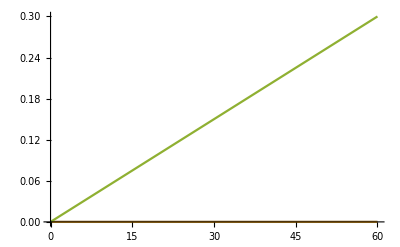

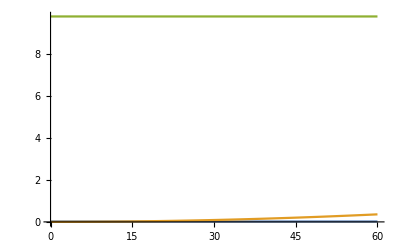

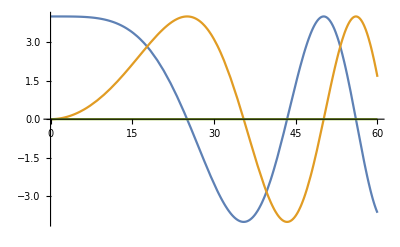

```mathematica
Plot[wR,{t,0,tloop}]
Plot[aR,{t,0,tloop}]
Plot[SW,{t,0,tloop}]
```

# Output

```mathematica
SetDirectory[NotebookDirectory[]];
Run["rm *.cppready"];
```

```mathematica
MyStringWrite[ToGoodC[N[GT]],"AnalyticTraj_UniformlyAcceleratedCircularMotion_GT.mthout"];
Run["python ../fixMathematicaOutput_v2.py AnalyticTraj_UniformlyAcceleratedCircularMotion_GT.mthout x 0 1"];

MyStringWrite[ToGoodC[x0],"AnalyticTraj_UniformlyAcceleratedCircularMotion_x0.mthout"];
Run["python ../fixMathematicaOutput_v2.py AnalyticTraj_UniformlyAcceleratedCircularMotion_x0.mthout x0 0 1"];
MyStringWrite[ToGoodC[x1],"AnalyticTraj_UniformlyAcceleratedCircularMotion_x1.mthout"];
Run["python ../fixMathematicaOutput_v2.py AnalyticTraj_UniformlyAcceleratedCircularMotion_x1.mthout x1 0 1"];

MyStringWrite[ToGoodC[N[SW]],"AnalyticTraj_UniformlyAcceleratedCircularMotion_gps.mthout"];
Run["python ../fixMathematicaOutput_v2.py AnalyticTraj_UniformlyAcceleratedCircularMotion_gps.mthout zgps 0 1"];

MyStringWrite[ToGoodC[N[wR]],"AnalyticTraj_UniformlyAcceleratedCircularMotion_w.mthout"];
Run["python ../fixMathematicaOutput_v2.py AnalyticTraj_UniformlyAcceleratedCircularMotion_w.mthout zw 0 1"];

MyStringWrite[ToGoodC[N[aR]],"AnalyticTraj_UniformlyAcceleratedCircularMotion_a.mthout"];
Run["python ../fixMathematicaOutput_v2.py AnalyticTraj_UniformlyAcceleratedCircularMotion_a.mthout za 0 1"];
```

```mathematica
Run["mv *.cppready ../../../roamfree/ROAMtest/generated"];

Run["rm *.cppready"];
Run["rm *.mthout"];
```